```mathematica
<<MaTeX`
```

### 2D Zernike moments

```mathematica
(* plotting staff, auxilary functions *)
(* convert expression (fucntion) from polar coordinates to cartesian *)
r2c[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>x/r}/.r^n_:>(x^2+y^2)^(n/2)] 
(*r2c3d[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>z/r, }/.r^n_:>(x^2+y^2+ z^2)^(n/2)] *)
(*  *)
zPlot[e_]:=With[{f= r2c[e]},DensityPlot[  f,{x,-1,1},{y,-1,1},RegionFunction:>(#1^2+#2^2≤1&), PlotPoints->12,Frame->False, ImageSize->120, ColorFunction->"BlueGreenYellow"]]
```

```mathematica
{maxX, maxY, maxZ} = {65,65, 65};
{dx, dy, dz} = {2/(maxX-1), 2/(maxY-1), 2/(maxZ-1)};

(* radial polynomials *)
(* n ≥ m , n - m is even *)
R[n_, m_, r_]:=Sum[((-1)^k(n-k)!)/(k! ((n+m)/2 - k)! ((n-m)/2 - k)!)r^(n - 2 k),{k,0, (n - m)/2,1}]

(* Zernike polynomials *)
Z[n_, m_,r_, θ_]:=ZernikeR[Abs@n,Abs@m,r]*If[m ≥0, Cos[m θ], Sin[Abs@m θ]] (*R[n, m, r]*) 
(* Zernike moments for given 2D img *)
A[n_, m_, IMG_] :=Abs[ (m+1)/π Sum[
IMG⟦(maxX - 1)/2 + x/dx+1,(maxY - 1)/2 +  y/dy + 1⟧ r2c[Z[n,m,r,θ]],
{x, -1,1, dx}, {y, -1, 1, dy}]]
```

```mathematica
LablAlig={-1.2, 1};
zernikeHarmonics = Grid[
{{Overlay[{zPlot[Z[0,0,r,θ]], MaTeX["Z^{"<>ToString[0]<>"}_{"<> ToString[0]<>"}", Magnification->1.5]}, Alignment->LablAlig]},

Flatten@Table[Overlay[{zPlot[Z[1,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[1]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-1, 1}}],

Table[Overlay[{zPlot[Z[2,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[2]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-2, 0, 2}}],

Table[Overlay[{zPlot[Z[3,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[3]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-3, -1, 1, 3}}],

Table[Overlay[{zPlot[Z[4,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[4]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-4, -2, 0, 2, 4}}]
}]
```

-Graphics--Graphics- |  |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"/imgs/zernike_mods.pdf",zernikeHarmonics]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/descriptors//imgs/zernike_mods.pdf

#### Test on the 2D points cloud

Test of orthogonality

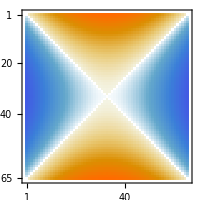

65

```mathematica
test2DOrt= Table[r2c[Z[2,2,r, θ]]//N(*If[Mod[i+j, 2] == 0, 1,0]*), {x,-1, 1, dx}, {y,-1,1, dy}];

MatrixPlot[test2DOrt, ImageSize->200]
Length@test2DOrt
```

```mathematica
Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,test2DOrt]//N},
{nm, {
{0,0}, 
{1,-1},{1,1}, 
{2,-2}, {2,0}, {2,2},
{3,-3},{3,-1},{3,1},{3,3},
{4,-4},{4,-2},{4,0},{4,2},{4,4}
}}]//TableForm
```

0 | 0 | 0.
1 | -1 | 0.
1 | 1 | 0.
2 | -2 | 0.
2 | 0 | 0.
2 | 2 | 762.246
3 | -3 | 0.
3 | -1 | 0.
3 | 1 | 0.
3 | 3 | 0.
4 | -4 | 0.
4 | -2 | 0.
4 | 0 | 0.
4 | 2 | 406.219
4 | 4 | 0.

```mathematica
(*generators *)
make2DPoint[i_,j_]:=Module[{pointOnPlane},
pointOnPlane = Table[0, {x,-Quotient[maxX,2], Quotient[maxY,2]}, {y,-Quotient[maxX,2], Quotient[maxY,2]}];
pointOnPlane⟦i, j⟧ = -1;

pointOnPlane⟦i, j+2⟧ = -2;
pointOnPlane⟦i, j-2⟧ = -2;
pointOnPlane⟦i+2, j⟧ = -1;
pointOnPlane⟦i-2, j⟧ = -1;
pointOnPlane⟦i-4, j⟧ = -1;

pointOnPlane
]
(* calculate mode indices *)
makeModIndices[n_]:=Table[{n, m}, {m, -n, n, 2}]
(* calcualte descriptor for given size of basis (for given number of harmonics) *)
makeDescriptorTable[IMG_, n_]:=Module[{table},
table = Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,IMG]//N},
{nm, Flatten[Table[makeModIndices[i],{i, 0, n}],1]}];
table//TableForm
]

makeDescriptorVector[IMG_, n_]:=Module[{table},
table = Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,IMG]//N},
{nm, Flatten[Table[makeModIndices[i],{i, 0, n}],1]}];
table
]
```

```mathematica
Manipulate[
Row[{MatrixPlot[make2DPoint[y,x], ImageSize->200], makeDescriptorTable[make2DPoint[x,y], 2]}],

{{x, (maxX-1)/2 + 1},1, maxX,1, Appearance->"Open"},
{{y, (maxY-1)/2 + 1},1, maxY,1, Appearance->"Open"}
]
```

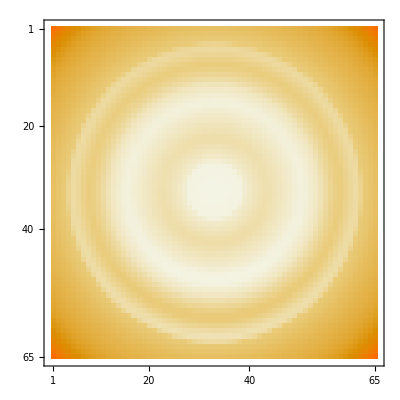

```mathematica
coeffs = makeDescriptorVector[make2DPoint[33,33], 10];
recover = Total[#⟦3⟧Table[r2c[Z[#⟦1⟧,#⟦2⟧,r, θ]]//N, {x,-1, 1, dx}, {y,-1,1, dy}]&/@coeffs];

MatrixPlot[recover]
```

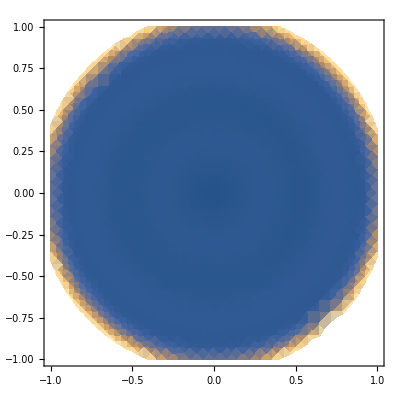

```mathematica
DensityPlot[Total[#⟦3⟧r2c[Z[#⟦1⟧,#⟦2⟧,r, θ]]&/@coeffs],{x,-1,1}, {y,-1,1}]
```

### 3D Zernike moments

```mathematica
(* definitions of 3D Zernike polynomials *)
(* normalization coefficients *)
c[m_, l_]:=(√((2 l + 1) (l + m)! (l-m)!))/(l!)
(* harmonic polynomials *)
e[m_, l_, x_, y_, z_]:=c[m, l] (x^2+y^2+z^2)^(l/2) ((ⅈ x- y)/2)^m z^(l -m) Sum[Binomial[l, k] Binomial[l-k, m + k] (-(x^2+y^2)/(4 z^2))^k, {k, 0, (l - m)/2}] 
q[ν_, k_, l_]:=(-1)^k/2^(2 k) √((2 l + 4 k + 3)/3) Binomial[2 k, k] (-1)^ν (Binomial[k, ν] Binomial[2 (k + l +ν) + 1, 2 k])/Binomial[k+l+ν, k]
(* n = [0, 1, 3, 4 ...] *)
(* l = [0, n] so that n - l is even number *)
(* m = [-l, l] *)
Z3[n_, l_, m_, x_, y_, z_]:=Sum[q[ν, (n-l)/2,l] (x^2+y^2+z^2)^ν e[m, l, x, y, z],{ν,0, (n-l)/2}]
(* 3D Zernike moment *)
A3[n_, l_, m_, IMG3_]:=3/(4 π)Abs@Sum[IMG3⟦(maxX - 1)/2 + x/dx+1,(maxY - 1)/2 +  y/dy + 1, (maxZ - 1)/2 +  z/dz + 1⟧, {x,-1, 1,dx},{y,-1, 1,dy},{z,-1, 1,dz}]
(* 3D Zernike descriptor *)
F3[n_, l_, IMG3_]:=Module[{collectedMHarmonics},
collectedMHarmonics = Table[A3[n, l, m, IMG3], {m,-l, l, 1}];
Norm[collectedMHarmonics]//N
]
```

```mathematica
(* generate mode indices *)
make3DModIndices[n_]:=Flatten[Table[{n, l, m}, {l,-n, n,2}, {m, -l, l}],1]
(* 3D Zernicke descriptors *)
makeDescriptorVector[IMG_, n_]:=Module[{table},
table = Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,IMG]//N},
{nm, Flatten[Table[makeModIndices[i],{i, 0, n}],1]}];
table
]
```

```mathematica
(* orthogonality check *)
Table[{{nlm⟦1⟧,nlm⟦2⟧,nlm⟦3⟧},{nlm1⟦1⟧,nlm1⟦2⟧,nlm1⟦3⟧},3/(4 π)Integrate[Z3[nlm⟦1⟧, nlm⟦2⟧, nlm⟦3⟧, x, y, z] Conjugate[Z3[nlm1⟦1⟧, nlm1⟦2⟧,nlm1⟦3⟧, x, y, z]], {x,-1,1},{y,-1,1}, {z,-1,1}]},{nlm, make3DModIndices[2]},{nlm1, make3DModIndices[2]}]
```

{{{{2,0,0},{2,0,0},112/(3 π)},{{2,0,0},{2,2,-2},0},{{2,0,0},{2,2,-1},0},{{2,0,0},{2,2,0},0},{{2,0,0},{2,2,1},0},{{2,0,0},{2,2,2},0}},{{{2,2,-2},{2,0,0},0},{{2,2,-2},{2,2,-2},187/(5 π)},{{2,2,-2},{2,2,-1},0},{{2,2,-2},{2,2,0},0},{{2,2,-2},{2,2,1},0},{{2,2,-2},{2,2,2},-341/(15 π)}},{{{2,2,-1},{2,0,0},0},{{2,2,-1},{2,2,-2},0},{{2,2,-1},{2,2,-1},902/(15 π)},{{2,2,-1},{2,2,0},0},{{2,2,-1},{2,2,1},0},{{2,2,-1},{2,2,2},0}},{{{2,2,0},{2,0,0},0},{{2,2,0},{2,2,-2},0},{{2,2,0},{2,2,-1},0},{{2,2,0},{2,2,0},44/(3 π)},{{2,2,0},{2,2,1},0},{{2,2,0},{2,2,2},0}},{{{2,2,1},{2,0,0},0},{{2,2,1},{2,2,-2},0},{{2,2,1},{2,2,-1},0},{{2,2,1},{2,2,0},0},{{2,2,1},{2,2,1},902/(15 π)},{{2,2,1},{2,2,2},0}},{{{2,2,2},{2,0,0},0},{{2,2,2},{2,2,-2},-341/(15 π)},{{2,2,2},{2,2,-1},0},{{2,2,2},{2,2,0},0},{{2,2,2},{2,2,1},0},{{2,2,2},{2,2,2},187/(5 π)}}}

```mathematica
make2DPoint[i_,j_, k_]:=Module[{pointOnPlane},
pointOnPlane = Table[0, {x,-Quotient[maxX,2], Quotient[maxY,2]}, {y,-Quotient[maxX,2], Quotient[maxY,2]}, {z,-Quotient[maxZ,2], Quotient[maxZ,2]}];
pointOnPlane⟦i, j, k⟧ = -1;
(*pointOnPlane⟦i, j, k-2⟧ = -1;
pointOnPlane⟦i, j, k+2⟧ = -1;*)
pointOnPlane
]
```

```mathematica
test3DOrt = make2DPoint[6,6,6];
```

```mathematica
F3[1,1,test3DOrt]
```

0.413497

```mathematica
DensityPlot3D[
Re[Z3[2,0,0, x,y,z]],
{x,-1, 1},
{y, -1, 1},
{z,-1, 1},
 PlotPoints->20,
ColorFunction->"BlueGreenYellow",
PlotRange->{{-1,1},{-1,1},{-1,1}}
]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
{DensityPlot3D[
Re[Z3[n,l,m, x,y,z]],
{x,-1, 1},
{y, -1, 1},
{z,-1, 1},
 PlotPoints->20,
PlotRange->{{-1,1},{-1,1},{-1,1}}
],
ListPointPlot3D[test3DOrt, PlotStyle->{PointSize[Large], Red},PlotRange->{{-1,1},{-1,1},{-1,1}}]
}
],
{{n, 0}, 0, 6, 1, Appearance->"Open"},
{{l, 0}, 0, 4, 2, Appearance->"Open"},
{{m, 0}, -l, l, 1, Appearance->"Open"}
]
```